```mathematica
(*

Testing Energy Statistics and comparing with K-means, GMM.

Guilherme S. Franca <guifranca@gmail.com>, 3/13/2017
  Johns Hopkins University

*)
```

```mathematica
(* 2 Clusters only *)

G[A_,B_,α_]:=(
Subscript[n, 1]=Length[A];
Subscript[n, 2]=Length[B];
g=1/(Subscript[n, 1] Subscript[n, 2])Sum[Norm[A[[i]]-B[[j]]]^α,{i,1,Subscript[n, 1]},{j,1,Subscript[n, 2]}];
Return[g];
)

Energy[A_,B_,α_]:=(
Subscript[n, 1]=Length[A];
Subscript[n, 2]=Length[B];
e=(Subscript[n, 1] Subscript[n, 2])/(Subscript[n, 1]+Subscript[n, 2])(2G[A,B,α]-G[A,A,α]-G[B,B,α]);
Return[e];
)

EnergyShuffle[A_,B_,n_]:=(
X1=Join[RandomSample[A,300-n],RandomSample[B,n]];
Y1=Join[RandomSample[B,300-n],RandomSample[A,n]];
Return[Energy[X1,Y1,1]];
)

J[A_,B_]:=(
Subscript[m, a]=Mean[A];
Subscript[m, b]= Mean[B];
Subscript[n, a]=Length[A];
Subscript[n, b]=Length[B];
j=1/2(Sum[Norm[A[[i]]-Subscript[m, a]]^2,{i,1,Length[A]}]+Sum[Norm[B[[i]]-Subscript[m, b]]^2,{i,1,Length[B]}]);
Return[j];
)

KmeansShuffle[A_,B_,n_]:=(
X1=Join[RandomSample[A,300-n],RandomSample[B,n]];
Y1=Join[RandomSample[B,300-n],RandomSample[A,n]];
Return[J[X1,Y1]];
)

GMM[A_,B_]:=(
Subscript[n, a]=Length[A];
Subscript[n, b]=Length[B];
Subscript[μ, a]=Mean[A];
Subscript[μ, b]=Mean[B];
Subscript[Σ, a]=Covariance[A];
Subscript[Σ, b]=Covariance[B];
l=Sum[Log[PDF[MultinormalDistribution[Subscript[μ, a],Subscript[Σ, a]],A[[n]]]],{n,1,Subscript[n, a]}]+Sum[Log[PDF[MultinormalDistribution[Subscript[μ, b],Subscript[Σ, b]],B[[n]]]],{n,1,Subscript[n, b]}];
Return[l];
)

GMMShuffle[A_,B_,n_]:=(
X1=Join[RandomSample[A,300-n],RandomSample[B,n]];
Y1=Join[RandomSample[B,300-n],RandomSample[A,n]];
Return[GMM[X1,Y1]];
)
```

```mathematica
X=RandomVariate[MultinormalDistribution[{0,0},{{1,0},{0,2}}],500];
Y=RandomVariate[MultinormalDistribution[{5,5},{{1,0},{0,1}}],500];
```

```mathematica
g1=ListPlot[{X,Y},AspectRatio->1];
g2=ListPlot[Table[{n,EnergyShuffle[X,Y,n]},{n,0,100,5}],AxesLabel->{"n","Ε"},PlotStyle->{PointSize[Medium], Blue}];
g3=ListPlot[Table[{n,KmeansShuffle[X,Y,n]},{n,0,100,5}],AxesLabel->{"n","J"},PlotStyle->{PointSize[Medium],Red}];
g4=ListPlot[Table[{n,GMMShuffle[X,Y,n]},{n,0,100,5}],AxesLabel->{"n","L"},PlotStyle->{PointSize[Medium],Darker[Green]}];
```

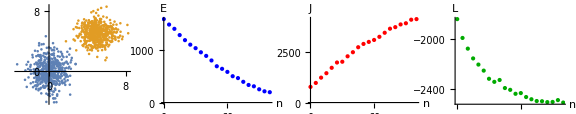

```mathematica
g=GraphicsGrid[{{g1,g2,g3,g4}},ImageSize->Large]
```

```mathematica
Export["C:\\Users\\guifr\\Desktop\\energy_kmeans_gmm_two_separate_gaussians.pdf",g,"PDF"]
```

C:\Users\guifr\Desktop\energy_kmeans_gmm_two_separate_gaussians.pdf

```mathematica
X=RandomVariate[MultinormalDistribution[{0,0},{{1,0},{0,1}}],500];
Y=RandomVariate[MultinormalDistribution[{0,0},{{2,1},{1,5}}],500];
```

```mathematica
g1=ListPlot[{X,Y},AspectRatio->1];
g2=ListPlot[Table[{n,EnergyShuffle[X,Y,n]},{n,0,100,5}],AxesLabel->{"n","Ε"},PlotStyle->{PointSize[Medium], Blue}];
g3=ListPlot[Table[{n,KmeansShuffle[X,Y,n]},{n,0,100,5}],AxesLabel->{"n","J"},PlotStyle->{PointSize[Medium],Red}];
g4=ListPlot[Table[{n,GMMShuffle[X,Y,n]},{n,0,100,5}],AxesLabel->{"n","L"},PlotStyle->{PointSize[Medium],Darker[Green]}];
```

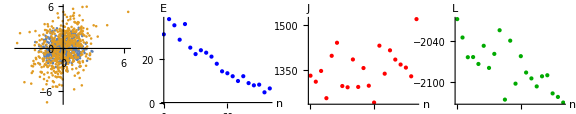

```mathematica
g=GraphicsGrid[{{g1,g2,g3,g4}},ImageSize->Large]
```

```mathematica
Export["C:\\Users\\guifr\\Desktop\\energy_kmeans_gmm_two_overlaping_gaussians.pdf",g,"PDF"]
```

C:\Users\guifr\Desktop\energy_kmeans_gmm_two_overlaping_gaussians.pdf

```mathematica
(* funny functions to generate data *)

G1[η_]:=(
t = RandomReal[{-1,1}];
v={10t,10 t^3+2 t^2-10t};
v=v+η RandomVariate[MultinormalDistribution[{0,0},{{1,0},{0,1}}]];
Return[v];
)
G2[η_]:=(
t = RandomReal[{0,4Pi}];
v={t Cos[t],t Sin[t]};
v=v+η RandomVariate[MultinormalDistribution[{0,0},{{1,0},{0,1}}]];
Return[v];
)
G3[η_]:=(
t = RandomReal[{0,4Pi}];
v={3 Cos[t],3 Sin[t],3t};
v=v+η RandomVariate[MultinormalDistribution[{0,0,0},{{1,0,0},{0,1,0},{0,0,1}}]];
Return[v];
)

G4[η_]:=(
t = RandomReal[{-1,1}];
v={10t+12,10 t^3+2 t^2-10t+1};
v=v+η RandomVariate[MultinormalDistribution[{0,0},{{1,0},{0,1}}]];
Return[v];
)
G5[η_]:=(
t = RandomReal[{0,4Pi}];
v={-t Cos[t],-t Sin[t]};
v=v+η RandomVariate[MultinormalDistribution[{0,0},{{1,0},{0,1}}]];
Return[v];
)
G6[η_]:=(
t = RandomReal[{0,4Pi}];
v={-Cos[t],- Sin[t],2t};
v=v+η RandomVariate[MultinormalDistribution[{0,0,0},{{1,0,0},{0,1,0},{0,0,1}}]];
Return[v];
)
```

```mathematica
GraphicsRow[{
ListPlot[{Table[G1[0.1],{i,1,400}],Table[G4[0.1],{i,1,400}]}],
ListPlot[{Table[G2[0.1],{i,1,500}],Table[G5[0.1],{i,1,500}]}],
ListPointPlot3D[{Table[G3[0.05],{i,1,400}],Table[G6[0.05],{i,1,400}]}]},ImageSize->Large]
```

-Graphics-

```mathematica
X=Table[G1[0.1],{i,1,500}];
Y=Table[G4[0.1],{i,1,500}];
```

```mathematica
g1=ListPlot[{X,Y},AspectRatio->1];
g2=ListPlot[Table[{n,EnergyShuffle[X,Y,n]},{n,0,100,5}],AxesLabel->{"n","Ε"},PlotStyle->{PointSize[Medium], Blue}];
g3=ListPlot[Table[{n,KmeansShuffle[X,Y,n]},{n,0,100,5}],AxesLabel->{"n","J"},PlotStyle->{PointSize[Medium],Red}];
g4=ListPlot[Table[{n,GMMShuffle[X,Y,n]},{n,0,100,5}],AxesLabel->{"n","L"},PlotStyle->{PointSize[Medium],Darker[Green]}];
```

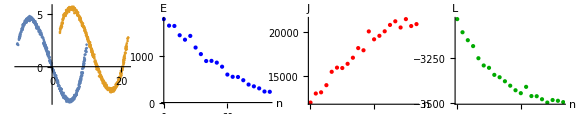

```mathematica
g=GraphicsGrid[{{g1,g2,g3,g4}},ImageSize->Large]
```

```mathematica
Export["C:\\Users\\guifr\\Desktop\\energy_kmeans_gmm_two_sinusoids.pdf",g,"PDF"]
```

C:\Users\guifr\Desktop\energy_kmeans_gmm_two_sinusoids_gaussians.pdf

```mathematica
X=Table[G2[0.1],{i,1,500}];
Y=Table[G5[0.1],{i,1,500}];
```

```mathematica
g1=ListPlot[{X,Y},AspectRatio->1];
g2=ListPlot[Table[{n,EnergyShuffle[X,Y,n]},{n,0,100,5}],AxesLabel->{"n","Ε"},PlotStyle->{PointSize[Medium], Blue}];
g3=ListPlot[Table[{n,KmeansShuffle[X,Y,n]},{n,0,100,5}],AxesLabel->{"n","J"},PlotStyle->{PointSize[Medium],Red}];
g4=ListPlot[Table[{n,GMMShuffle[X,Y,n]},{n,0,100,5}],AxesLabel->{"n","L"},PlotStyle->{PointSize[Medium],Darker[Green]}];
```

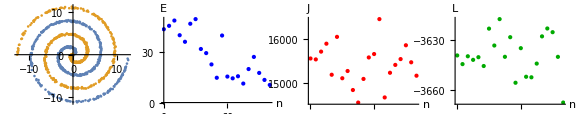

```mathematica
g=GraphicsGrid[{{g1,g2,g3,g4}},ImageSize->Large]
```

```mathematica
Export["C:\\Users\\guifr\\Desktop\\energy_kmeans_gmm_two_spirals.pdf",g,"PDF"]
```

C:\Users\guifr\Desktop\energy_kmeans_gmm_two_spirals.pdf

```mathematica
X=Table[G3[0.05],{i,1,500}];
Y=Table[G6[0.05],{i,1,500}];
```

```mathematica
g17=ListPointPlot3D[{X,Y},AspectRatio->1];
g18=ListPlot[Table[{n,EnergyShuffle[X,Y,n]},{n,0,100,5}],AxesLabel->{"n","Ε"},PlotStyle->{Blue,PointSize[Medium]}];
g19=ListPlot[Table[{n,KmeansShuffle[X,Y,n]},{n,0,100,5}],AxesLabel->{"n","Ε"},PlotStyle->{Red,PointSize[Medium]}];
g20=ListPlot[Table[{n,GMMShuffle[X,Y,n]},{n,0,100,5}],AxesLabel->{"n","Ε"},PlotStyle->{Darker[Green],PointSize[Medium]}];
```

```mathematica
GraphicsGrid[{{g17,g18,g19,g20}},ImageSize->Large]
```

-Graphics-

```mathematica
g=GraphicsGrid[{
{g1,g2,g3,g4},
{g5,g6,g7,g8},
{g9,g10,g11,g12},
{g13,g14,g15,g16},
{g17,g18,g19,g20}
},ImageSize->900]
```

```mathematica
Export["C:\\Users\\guifr\\Desktop\\energy_kmeans_gmm.pdf",g,"PDF"]
```

C:\Users\guifr\Desktop\energy_kmeans_gmm.pdf

```mathematica
(* Arbitrary Number of Clusters *)

(* Energy Statistics Function *)
G[A_,B_,α_]:=(
Subscript[n, a]=Length[A];
Subscript[n, b]=Length[B];
g=1/(Subscript[n, a] Subscript[n, b])Sum[Norm[A[[i]]-B[[j]]]^α,{i,1,Subscript[n, a]},{j,1,Subscript[n, b]}];
Return[g];
)
Sn[A_,α_]:=(
M=Sum[Length[A[[i]]],{i,1,Length[A]}];
For[i=1;s=0,i≤Length[A],i++,
n=Length[A[[i]]];
For[j=i+1,j≤Length[A],j++,
m=Length[A[[j]]];
s=s+(n m)/(2 M)( 2G[A[[i]],A[[j]],α]-G[A[[i]],A[[i]],α]-G[A[[j]],A[[j]],α] );
];
];
Return[s];
)

(* K-means objective function *)
Jn[A_]:=(
M=Sum[Length[A[[i]]],{i,1,Length[A]}];
For[i=1;e=0,i≤Length[A],i++,
m=Mean[A[[i]]];
e=e+1/2 Sum[Norm[A[[i]][[j]]-m]^2,{j,1,Length[A[[i]]]}];
];
Return[e/M];
)

(* GMM Log-likelihood function *)
Ln[A_]:=(
M=Sum[Length[A[[i]]],{i,1,Length[A]}];
For[i=1;e=0,i≤Length[A],i++,
μ=Mean[A[[i]]];
Σ=Covariance[A[[i]]];
e=e+Sum[Log[PDF[MultinormalDistribution[μ,Σ],A[[i]][[n]]]],{n,1,Length[A[[i]]]}];
];
Return[e/M];
)

(* Mixing data from different components. A is the pooled sample. *)
Shuffle[A_,n_]:=(
(* Let K be the number of components of A. Let N be the minimum number of points in each coponenent. Make sure that N is larger than n(K-1) or this function will crash.  *)
m=Length[A];
B=Table[RandomSample[A[[i]],Length[A[[i]]]-n(m-1)],{i,1,m}];
For[i=1,i≤m,i++,
For[j=1,j≤m ,j++,
B[[i]]=If[j≠i,Join[B[[i]],RandomSample[A[[j]],n]],B[[i]]];
];
];
Return[B];
);
```

```mathematica
data={
RandomVariate[MultinormalDistribution[{0,0},{{1,0},{0,1}}],500],RandomVariate[MultinormalDistribution[{0,0},{{.5,0.1},{0.1,.5}}],500],
RandomVariate[MultinormalDistribution[{0.5,0.5},{{.5,0},{0,.5}}],500]
};
```

```mathematica
g1=ListPlot[data,AspectRatio->1];
g2=ListPlot[Table[{n,Sn[Shuffle[data,n],1]},{n,0,100,5}],AxesLabel->{"n","Ε"},PlotStyle->{Blue,PointSize[Medium]}];
g3=ListPlot[Table[{n,Jn[Shuffle[data,n]]},{n,0,100,5}],AxesLabel->{"n","J"},PlotStyle->{Red,PointSize[Medium]}];
g4=ListPlot[Table[{n,Ln[Shuffle[data,n]]},{n,0,100,5}],AxesLabel->{"n","L"},PlotStyle->{Darker[Green],PointSize[Medium]}];
```

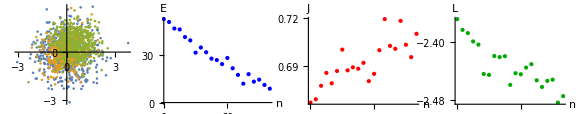

```mathematica
g=GraphicsRow[{g1,g2,g3,g4},ImageSize->Large]
```

```mathematica
Export["C:\\Users\\guifr\\Desktop\\energy_kmeans_gmm_three_overlaping_gaussians.pdf",g,"PDF"]
```

C:\Users\guifr\Desktop\energy_kmeans_gmm_three_overlaping_gaussians.pdf

```mathematica
Spiral[η_,a_,b_,k_]:=(
t = RandomReal[{0,2 k Pi}];
v={a t Cos[t],b t Sin[t]};
v=v+η RandomVariate[MultinormalDistribution[{0,0},{{1,0},{0,1}}]];
Return[v];
)
```

```mathematica
data={
Table[Spiral[.2,1,1,2],{i,1,500}],
Table[Spiral[.25,-1,-1,2],{i,1,500}],
Table[Spiral[.3,1,-1,2],{i,1,500}]
};
```

```mathematica
g1=ListPlot[data,AspectRatio->1];
g2=ListPlot[Table[{n,Sn[Shuffle[data,n],1]},{n,0,100,5}],AxesLabel->{"n","Ε"},PlotStyle->{Blue,PointSize[Medium]}];
g3=ListPlot[Table[{n,Jn[Shuffle[data,n]]},{n,0,100,5}],AxesLabel->{"n","Ε"},PlotStyle->{Red,PointSize[Medium]}];
g4=ListPlot[Table[{n,Ln[Shuffle[data,n]]},{n,0,100,5}],AxesLabel->{"n","Ε"},PlotStyle->{Darker[Green],PointSize[Medium]}];
```

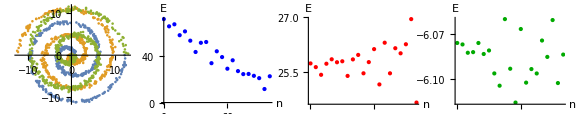

```mathematica
g=GraphicsRow[{g1,g2,g3,g4},ImageSize->Large]
```

```mathematica
Export["C:\\Users\\guifr\\Desktop\\energy_kmeans_gmm_three_spirals.pdf",g,"PDF"]
```

C:\Users\guifr\Desktop\energy_kmeans_gmm_three_spirals.pdf

```mathematica
(* Testing High Dimensions *)

dims=Table[i,{i,2,70,10}]
g={};
For[k=1,k≤Length[dims],k++,
d=dims[[k]];
m=70;
Print[k];
m1=Table[0,{i,1,d}];
m2=m1; m2[[1]]=2; 
s1=IdentityMatrix[d];
s2=.5*IdentityMatrix[d];
data={
RandomVariate[MultinormalDistribution[m1,s1],m],
RandomVariate[MultinormalDistribution[m2,s2],m]
};
g=Append[g,ListPlot[Table[{n,Sn[Shuffle[data,n],1]},{n,0,30,2}],AxesLabel->{"n","Ε"},PlotStyle->{Blue,PointSize[Medium]}]];
g=Append[g,ListPlot[Table[{n,Jn[Shuffle[data,n]]},{n,0,30,2}],AxesLabel->{"n","J"},PlotStyle->{Red,PointSize[Medium]}]];
g=Append[g,ListPlot[Table[{n,Ln[Shuffle[data,n]]},{n,0,30,2}],AxesLabel->{"n","L"},PlotStyle->{Darker[Green],PointSize[Medium]}]];
];
```

{2,12,22,32,42,52,62}

1

2

3

4

5

6

7

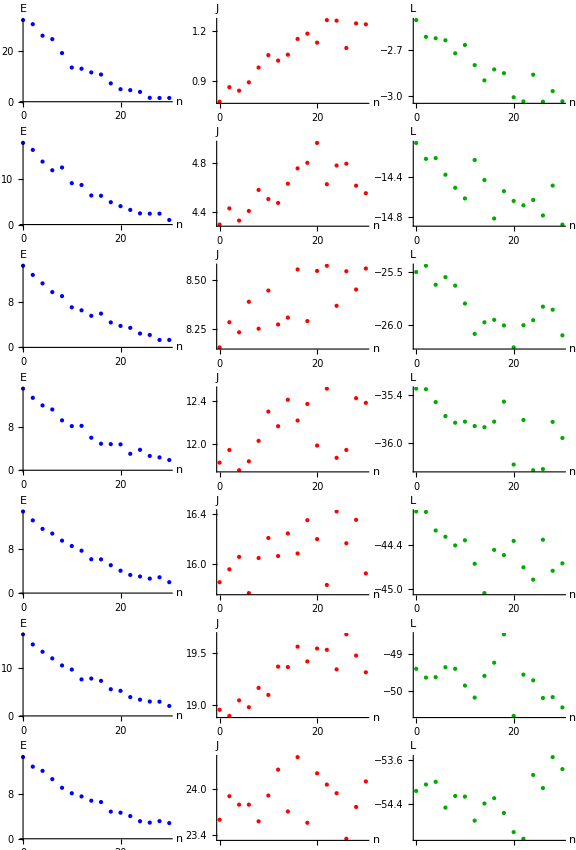

```mathematica
a=GraphicsGrid[Table[g[[i;;i+2]],{i,1,21,3}],ImageSize->Large]
```

```mathematica
Export["C:\\Users\\guifr\\Desktop\\two_separate_gaussians_increasing_dimensions.pdf",a,"PDF"]
```

C:\Users\guifr\Desktop\two_separate_gaussians_increasing_dimensions.pdf

```mathematica
H=Table[If[i==j,1,0]-1/3,{i,1,3},{j,1,3}];
H//MatrixForm
```

(2/3 | -1/3 | -1/3
-1/3 | 2/3 | -1/3
-1/3 | -1/3 | 2/3)

```mathematica
H.H//MatrixForm
```

(2/3 | -1/3 | -1/3
-1/3 | 2/3 | -1/3
-1/3 | -1/3 | 2/3)